# Modelización Matemática - Tema 5

## Diego Ángel Gallardo Costilla

```mathematica
Clear[x,t,a,r,y,e,q]
```

```mathematica
a=1;b=0.5;c=0.75;d=0.25
```

0.25

```mathematica
eq1:=x'[t] == a x[t] - b x[t] y[t];
eq2:=y'[t]==-c y[t]  + d x[t] y[t];
ci = {x[0]==10,y[0]==5}
```

{x[0]==10,y[0]==5}

```mathematica
NDSolve[{eq1,eq2,ci},{x,y},{t,0,50}]
```

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…]}}

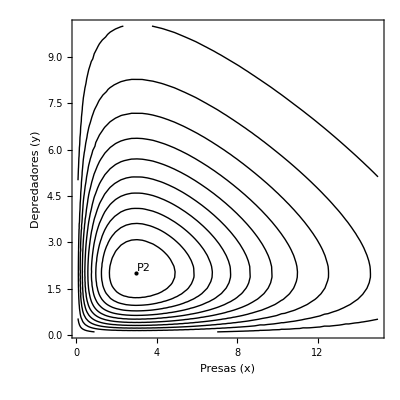

```mathematica
p2={c/d,a/b};
f[x_,y_]:=(y^a)*(x^c)*Exp[-d*x-b*y]
ContourPlot[f[x,y],{x,0.1,15},{y,0.1,10},Contours->10,ContourShading->None,FrameLabel->{"Presas (x)","Depredadores (y)"},Epilog->{PointSize[Large],Point[p2],Text["P2",p2,{-1.5,-1.5}]}]
```